```mathematica
Depolarizing Error;
```

```mathematica
Error={#.State1.ConjugateTranspose[#],#.State2.ConjugateTranspose[#],#.State3.ConjugateTranspose[#],#.State4.ConjugateTranspose[#]}&;
Error2={#1.State1.ConjugateTranspose[#1],#2.State2.ConjugateTranspose[#2],#3.State3.ConjugateTranspose[#3],#4.State4.ConjugateTranspose[#4]}&;
Error2prob={probability1#1.State1.ConjugateTranspose[#1],probability3 #2.State2.ConjugateTranspose[#2],probability5#3.State3.ConjugateTranspose[#3],probability7 #4.State4.ConjugateTranspose[#4]}&;
ErrorM2prob={probabilityM1#1.State1.ConjugateTranspose[#1],probabilityM3 #2.State2.ConjugateTranspose[#2],probabilityM5#3.State3.ConjugateTranspose[#3],probabilityM7 #4.State4.ConjugateTranspose[#4]}&;

Clear[probability0,probability1,probability2,probability3,probability4,probability5,probability6,probability7,probabilityM1,probabilityM2,probabilityM3,probabilityM4,probabilityM5,probabilityM6,probabilityM7]

DepolarizingError=Error2[X+Y+Z, X+Y+Z,X+Y+Z,X+Y+Z];
DepolarizingError8=Error2prob[X+Y+Z, X+Y+Z,X+Y+Z,X+Y+Z];
DepolarizingErrorM8=ErrorM2prob[X+Y+Z, X+Y+Z,X+Y+Z,X+Y+Z];
```

```mathematica
LogPlots1qubit8probabilitiesDepolarizingError3[Gate_,title_]:=Module[{IErrorFidelity,MErrorFidelity,IErrorFidelitys,MErrorFidelitys,IMErrorFidelity,MeasuFidelitys},
Clear[probability0,probability1,probability2,probability3,probability4,probability5,probability6,probability7,probability8,probability9,probability10,probability11,probability12,probability13,probability14,probability15];
IErrorFidelitys=FindASetOfProbabilitiesAndFidelityInput8probabilities1qubit[Pideal1qubit,Sideal1qubit,AI1qubit,Gate,DepolarizingError8];
Clear[probability0,probability1,probability2,probability3,probability4,probability5,probability6,probability7];
MeasuFidelitys=FindASetOfProbabilitiesAndFidelityMeasurement8probabilities1qubit[Pideal1qubit,Sideal1qubit,AI1qubit,Gate,DepolarizingError8];
Clear[probability0,probability1];
IErrorFidelity=FindASetOfProbabilitiesAndFidelityInput2probabilities1qubit[Pideal1qubit,Sideal1qubit,AI1qubit,Gate,DepolarizingError];
Clear[probability0,probability1];
ErrorFidelity=FindASetOfProbabilitiesAndFidelityMeasurement2probabilities1qubit[Pideal1qubit,Sideal1qubit,AI1qubit,Gate,DepolarizingError];
Clear[probability0,probability1,probabilityM0,probabilityM1];

Clear[probability0,probability1,probability2,probability3,probabilityM1,probabilityM2,probabilityM3];
IMErrorFidelity=FindASetOfProbabilitiesAndFidelityInputMeasurement2probabilities1qubit[Pideal1qubit,Sideal1qubit,AI1qubit,Gate,DepolarizingError];

LogPlotResults5[IErrorFidelity,ErrorFidelity,IErrorFidelitys,MeasuFidelitys,ImErrorFidelity,3,2,2,"Infidelity",title]]
```

```mathematica
LogPlots1qubit8probabilitiesDepolarizingError3Complex[Gate_,title_]:=Module[{IErrorFidelity,MErrorFidelity,IErrorFidelitys,MErrorFidelitys,IMErrorFidelity,MeasuFidelitys},
Clear[probability0,probability1,probability2,probability3,probability4,probability5,probability6,probability7,probability8,probability9,probability10,probability11,probability12,probability13,probability14,probability15];
IErrorFidelitys=FindASetOfProbabilitiesAndFidelityInput8probabilities1qubit[Pideal1qubit,Sideal1qubit,AI1qubit,Gate,DepolarizingError8];
Clear[probability0,probability1,probability2,probability3,probability4,probability5,probability6,probability7];
MeasuFidelitys=FindASetOfProbabilitiesAndFidelityMeasurement8probabilities1qubit[Pideal1qubit,Sideal1qubit,AI1qubit,Gate,DepolarizingError8];
Clear[probability0,probability1];
IErrorFidelity=FindASetOfProbabilitiesAndFidelityInput2probabilities1qubit[Pideal1qubit,Sideal1qubit,AI1qubit,Gate,DepolarizingError];
Clear[probability0,probability1];
ErrorFidelity=FindASetOfProbabilitiesAndFidelityMeasurement2probabilities1qubit[Pideal1qubit,Sideal1qubit,AI1qubit,Gate,DepolarizingError];
Clear[probability0,probability1,probabilityM0,probabilityM1];

Clear[probability0,probability1,probability2,probability3,probabilityM1,probabilityM2,probabilityM3];
IMErrorFidelity=FindASetOfProbabilitiesAndFidelityInputandMeasurement8probabilities1qubit[Pideal1qubit,Sideal1qubit,AI1qubit,Gate,DepolarizingError8,DepolarizingErrorM8];

LogPlotResults5[IErrorFidelity,ErrorFidelity,IErrorFidelitys,MeasuFidelitys,IMErrorFidelity,3,2,2,"Infidelity",title]]
```

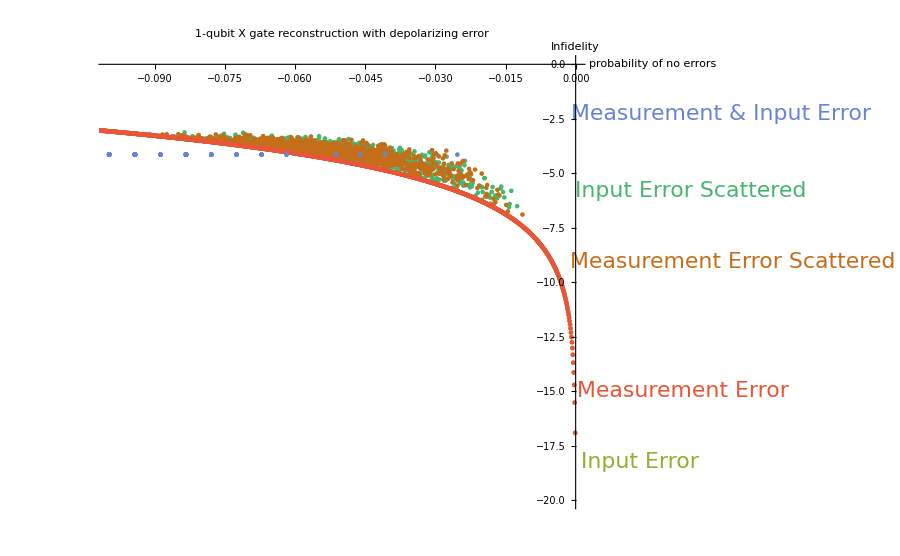

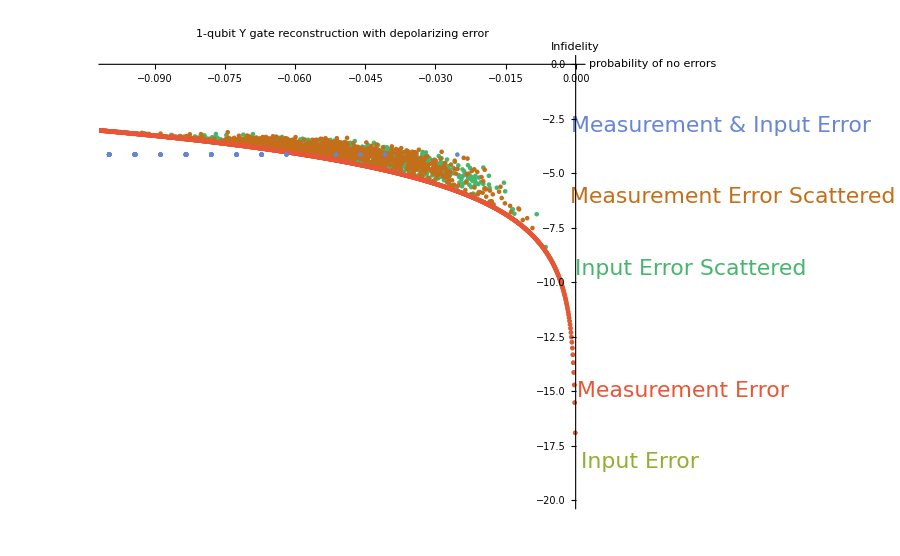

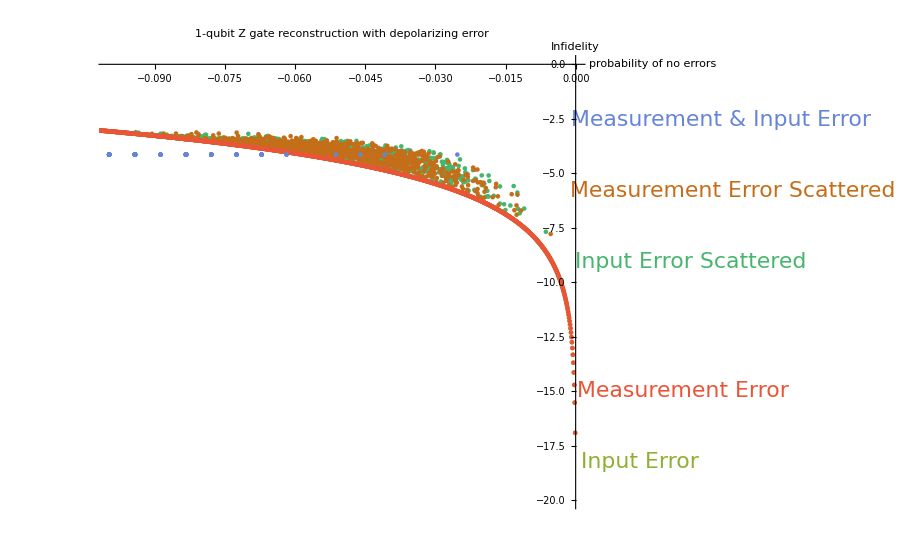

```mathematica
LogPlots1qubit8probabilitiesDepolarizingError3[X,"1-qubit X gate reconstruction with depolarizing error"]
LogPlots1qubit8probabilitiesDepolarizingError3[Y,"1-qubit Y gate reconstruction with depolarizing error"]
LogPlots1qubit8probabilitiesDepolarizingError3[Z,"1-qubit Z gate reconstruction with depolarizing error"]
```

```mathematica
LogPlots1qubit8probabilitiesDepolarizingError3Complex[X,"1-qubit X gate reconstruction with depolarizing error"]
LogPlots1qubit8probabilitiesDepolarizingError3Complex[Y,"1-qubit Y gate reconstruction with depolarizing error"]
LogPlots1qubit8probabilitiesDepolarizingError3Complex[Z,"1-qubit Z gate reconstruction with depolarizing error"]
```